[1/3] Generating Computational Universe (Steps: 1000)...

[2/3] Simulating Wave Propagation...

[3/3] Calculating Quantum vs. Classical Distributions...

Screen Nodes Found: 67

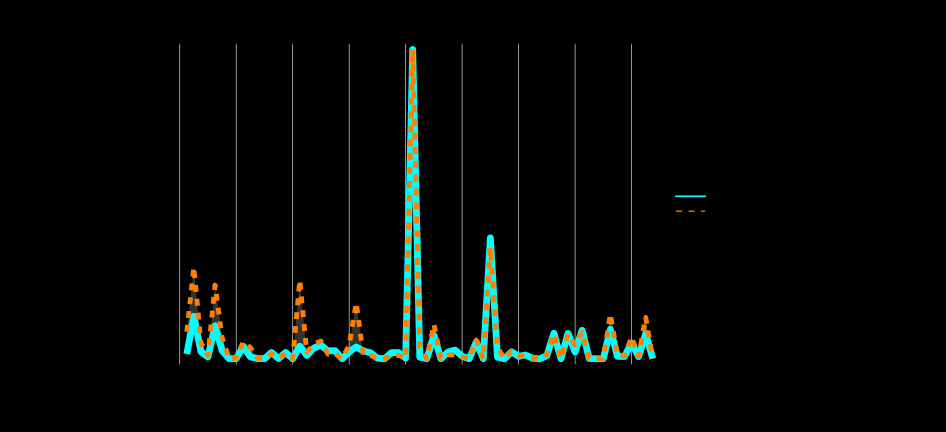

```mathematica
(* ====================================================================*)(*COMPUTATIONAL UNIVERSE:WAVE-PARTICLE DUALITY (ROBUST VERSION)*)(* ====================================================================*)(*---PART 1:UNIVERSE GENERATION---*)rccRigidStep[g_Graph]:=Module[{allEdges,activeEdges,selectedPair,e1,e2,x,y,z,w,nextV,newActiveEdges,inertEdges},allEdges=EdgeList[g];
activeEdges=Cases[allEdges,_UndirectedEdge];
(*Optimization:Random sample to find pairs faster*)Block[{shuffled=RandomSample[activeEdges]},Do[e1=shuffled[[i]];
Do[e2=shuffled[[j]];
If[Length[Intersection[List@@e1,List@@e2]]==1,selectedPair={e1,e2};
Goto["Found"];],{j,i+1,Min[i+15,Length[shuffled]]}],{i,1,Length[shuffled]}]];
Label["Found"];
If[Not[ValueQ[selectedPair]],Return[g]];
{e1,e2}=selectedPair;
y=Intersection[List@@e1,List@@e2][[1]];
x=Complement[List@@e1,{y}][[1]];
z=Complement[List@@e2,{y}][[1]];
w=Max[VertexList[g]]+1;
newActiveEdges={x<->z,x<->w,w<->z};
(*History points to the past,but we will symmetrize later for physics*)inertEdges={x->y,z->y};
Graph[VertexList[g]~Join~{w},Union[Complement[allEdges,{e1,e2}],newActiveEdges,inertEdges]]];

(*Generate Universe*)
steps=1000;
initG=CycleGraph[4];
Print["[1/3] Generating Computational Universe (Steps: ",steps,")..."];
universe=Nest[rccRigidStep,initG,steps];

(*---PART 2:THE PHYSICS ENGINE (CORRECTED)---*)
Print["[2/3] Simulating Wave Propagation..."];

(*!!!CRITICAL FIX!!!*)
(*Convert to UNDIRECTED graph for wave propagation.*)
(*This allows waves to flow'against' the arrow of time (Back-reaction/Entanglement)*)
physicsUniverse=UndirectedGraph[universe];

nodeList=VertexList[physicsUniverse];
numNodes=Length[nodeList];

(*Select Sources:Pick nodes that are definitely highly connected*)
(*Instead of hardcoded indices,pick nodes based on degree to ensure they act as good sources*)
sortedByDegree=SortBy[nodeList,VertexDegree[physicsUniverse,#]&];
source1=sortedByDegree[[-1]]; (*Highest degree node (Hub)*)
source2=sortedByDegree[[-5]]; (*Another high degree node*)

(*Laplacian Operator (Symmetric/Hermitian)*)
adj=AdjacencyMatrix[physicsUniverse];
deg=DiagonalMatrix[VertexDegree[physicsUniverse]];
laplacian=N[deg-adj];
dt=0.05;
T=100; (*Evolution time*)

(*Propagate Function*)
propagate[src_]:=Module[{psi,accum},psi=ConstantArray[0.0+0.0 I,numNodes];
psi[[src]]=1.0;
accum=ConstantArray[0.0,numNodes];
Do[psi=psi-I*dt*(laplacian.psi);
psi=psi/Norm[psi];
(*Accumulate only the tail end to stabilize pattern*)If[t>T-50,accum+=psi];,{t,1,T}];
accum];

(*Run Independent Simulations*)
psi1=propagate[source1];
psi2=propagate[source2];

(*---PART 3:VISUALIZATION---*)
Print["[3/3] Calculating Quantum vs. Classical Distributions..."];

(*Define Screen:Nodes at a fixed hop-distance from Source 1*)
(*We try a range of distances to find a good'screen' layer*)
screenDist=8; (*Try 8 hops*)
screenNodes=Select[nodeList,GraphDistance[physicsUniverse,source1,#]==screenDist&];

(*Fallback if screen is empty (just in case)*)
If[Length[screenNodes]<10,Print["Adjusting screen distance..."];
screenDist=6;
screenNodes=Select[nodeList,GraphDistance[physicsUniverse,source1,#]==screenDist&];];

Print["Screen Nodes Found: ",Length[screenNodes]];

(*Calculate Data*)
screenData=Table[With[{d1=GraphDistance[physicsUniverse,source1,n],d2=GraphDistance[physicsUniverse,source2,n]},{d1-d2,n}],{n,screenNodes}];

(*Filter and Sort*)
screenData=Select[screenData,IntegerQ[First[#]]&];
sortedNodes=Last/@SortBy[screenData,First];

(*PROBABILITY CALCULATION*)
(*1. Quantum: |Psi1+Psi2|^2*)
probQuantum=Abs[psi1[[sortedNodes]]+psi2[[sortedNodes]]]^2;
(*2. Classical: |Psi1|^2+ |Psi2|^2*)
probClassical=Abs[psi1[[sortedNodes]]]^2+Abs[psi2[[sortedNodes]]]^2;

(*Plot*)
ListLinePlot[{Rescale[probQuantum],Rescale[probClassical]},PlotRange->All,PlotStyle->{{Thickness[0.007],Directive[RGBColor[0,1,1],Opacity[1]]},{Thickness[0.005],Directive[Orange,Dashed]}},PlotLegends->Placed[{Style["Quantum Wave (Interference)",14,Bold,RGBColor[0,1,1]],Style["Classical Particles (Collapse)",14,Bold,Orange]},{Right,Top}],Filling->{1->{2}},FillingStyle->Directive[Opacity[0.2],White],PlotLabel->Style["Emergent Wave-Particle Duality\n(Undirected Path Integral)",20,Bold,White],Frame->True,FrameLabel->{Style["Path Difference (d1 - d2)",15,White],Style["Probability Density",15,White]},FrameTicks->{Automatic,None},FrameStyle->Directive[White,Thickness[0.002]],GridLines->{Automatic,None},GridLinesStyle->Directive[Gray,Dashed],Background->Black,ImageSize->700,BaseStyle->{FontFamily->"Arial",FontSize->14}]
```